```mathematica
(*Parameters*)
γ=150; 
Dil=0.5; 
R0=0.5; 
ma=0.01; mb=0.1;mc=0.05; (*Example values for m parameters*)
TI=20;
δ = 0.5;

(*Define Imax and m as before*)
Imax[T_]:=Exp[-((T-TI)^2)/γ];
m[T_]:=ma Exp[mb T]+mc;

(*Function for Req and Ce*)
ReqFunc[T_]:=m[T] R0/((1-δ) Imax[T]-m[T]);
CeFunc[T_, Req_, S_]:=Dil (S-Req)(Req + R0)/(Imax[T] Req);

(*Perform a simulation with independent draws for Req and T*)
numSimulations=100000; (*Number of simulations*)

simulationResults=Table[
Module[
{S,T, Ce, ReqVal},
(*Draw values for Req and T*)
S=RandomVariate[NormalDistribution[1.5,0.2]];
T=RandomVariate[NormalDistribution[20,5]];
(*Calculate Req and Ce based on S and T*)
ReqVal = ReqFunc[T];
Ce=CeFunc[T,ReqVal,S];
 If[Ce < 0, Ce = 0];
{S,T, Ce, ReqVal}  (*Return the values*)],{numSimulations}];
(*Calculate the 95th percentile*)
minValue=Min[simulationResults];
percentile95=Quantile[simulationResults[[All, 3]],0.95];
```

```mathematica
(*Sensitivity Analysis Function with transparent scatter plot points*)sensitivityAnalysis[meanS_,varS_,meanT_,varT_]:=Module[{simulationResults,hist,scatterPlotS,scatterPlotT,pdfPlotS,pdfPlotT,weirdReq},(*Perform simulation with specified parameters for S and T*)simulationResults=Table[Module[{S,T,Ce,ReqVal},S=RandomVariate[NormalDistribution[meanS,varS]];(*Adjust mean and variance of S*)T=RandomVariate[NormalDistribution[meanT,varT]];(*Adjust mean and variance of T*)ReqVal=ReqFunc[T];
Ce=CeFunc[T,ReqVal,S];
If[Ce<0,Ce=0];
{S,T,Ce,ReqVal}],{numSimulations}];
(*Filter out invalid Req values*)weirdReq=Select[simulationResults,#[[4]]>0&];
(*Generate standard plots*)hist=Histogram[weirdReq[[All,3]],{-1,10,0.1},"Probability",PlotLabel->Style[Text@StringJoin["Histogram of Ce for S~Normal(",ToString[meanS],", ",ToString[varS],") and T~Normal(",ToString[meanT],", ",ToString[varT],")"],14]];
(*Scatter Plot of S vs Ce with transparent points*)scatterPlotS=ListPlot[weirdReq[[All,{1,3}]],PlotStyle->{Red,Opacity[0.1]},(*Make points transparent with Opacity*)AxesLabel->{"S","Ce"},FrameLabel->{"S","Ce"},LabelStyle->13,PlotLabel->Style[Text@StringJoin["S~Normal(",ToString[meanS],", ",ToString[varS],") vs Ce"],20],TicksStyle->Directive[FontSize->15],ImageSize->Large];
(*Scatter Plot of T vs Ce with transparent points*)scatterPlotT=ListPlot[weirdReq[[All,{2,3}]],PlotStyle->{Blue,Opacity[0.1]},(*Make points transparent with Opacity*)AxesLabel->{"T","Ce"},FrameLabel->{"T","Ce"},LabelStyle->13,PlotLabel->Style[Text@StringJoin["T~Normal(",ToString[meanT],", ",ToString[varT],") vs Ce"],20],TicksStyle->Directive[FontSize->15],ImageSize->Large];
(*Probability Density Function plots for S and T*)pdfPlotS=Plot[PDF[NormalDistribution[meanS,varS],x],{x,0,3},PlotLabel->Style[Text@StringJoin["PDF of S~Normal(",ToString[meanS],", ",ToString[varS],")"],14],Filling->Axis,PlotStyle->Red,AxesLabel->{"S","Density"},ImageSize->Medium];
pdfPlotT=Plot[PDF[NormalDistribution[meanT,varT],x],{x,0,40},PlotLabel->Style[Text@StringJoin["PDF of T~Normal(",ToString[meanT],", ",ToString[varT],")"],14],Filling->Axis,PlotStyle->Blue,AxesLabel->{"T","Density"},ImageSize->Medium];
(*Combine the plots into a single grid layout*)GraphicsGrid[{{pdfPlotS,pdfPlotT},{hist},{scatterPlotS},(*Scatter plot of S*){scatterPlotT}   (*Scatter plot of T*)},Spacings->{1,2}]]

(*Example usage with different mean and variance*)
```

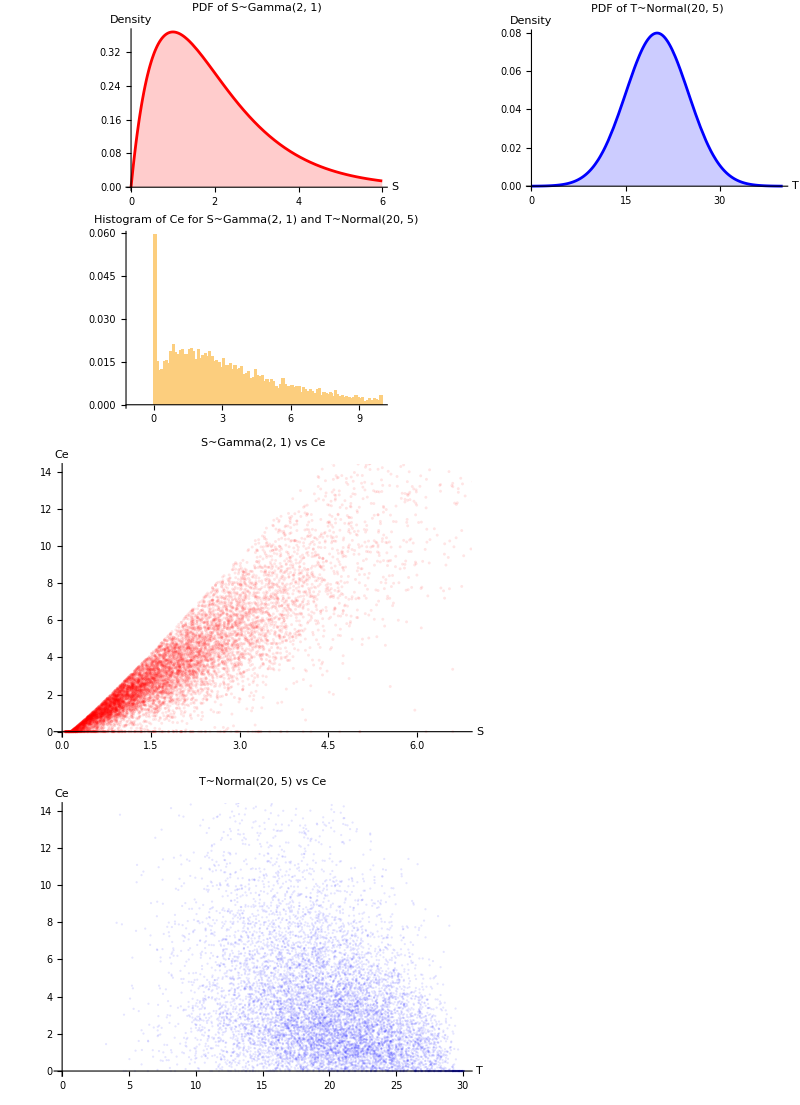

```mathematica
(*Sensitivity Analysis with Gamma and Normal distributions and transparent points*)sensitivityAnalysisGamma[alphaS_,betaS_,meanT_,varT_]:=Module[{simulationResults,hist,scatterPlotS,scatterPlotT,pdfPlotS,pdfPlotT,weirdReq},(*Perform simulation with Gamma distribution for S and Normal distribution for T*)simulationResults=Table[Module[{S,T,Ce,ReqVal},S=RandomVariate[GammaDistribution[alphaS,betaS]];(*Gamma distribution for S*)T=RandomVariate[NormalDistribution[meanT,varT]];(*Adjust mean and variance of T*)ReqVal=ReqFunc[T];
Ce=CeFunc[T,ReqVal,S];
If[Ce<0,Ce=0];
{S,T,Ce,ReqVal}],{numSimulations}];
(*Filter out invalid Req values*)weirdReq=Select[simulationResults,#[[4]]>0&];
(*Generate standard plots*)hist=Histogram[weirdReq[[All,3]],{-1,10,0.1},"Probability",PlotLabel->Style[Text@StringJoin["Histogram of Ce for S~Gamma(",ToString[alphaS],", ",ToString[betaS],") and T~Normal(",ToString[meanT],", ",ToString[varT],")"],14]];
(*Scatter Plot of S vs Ce with transparent points*)scatterPlotS=ListPlot[weirdReq[[All,{1,3}]],PlotStyle->{Red,Opacity[0.1]},(*Make points transparent with Opacity*)AxesLabel->{"S","Ce"},FrameLabel->{"S","Ce"},LabelStyle->13,PlotLabel->Style[Text@StringJoin["S~Gamma(",ToString[alphaS],", ",ToString[betaS],") vs Ce"],20],TicksStyle->Directive[FontSize->15],ImageSize->Large];
(*Scatter Plot of T vs Ce with transparent points*)scatterPlotT=ListPlot[weirdReq[[All,{2,3}]],PlotStyle->{Blue,Opacity[0.1]},(*Make points transparent with Opacity*)AxesLabel->{"T","Ce"},FrameLabel->{"T","Ce"},LabelStyle->13,PlotLabel->Style[Text@StringJoin["T~Normal(",ToString[meanT],", ",ToString[varT],") vs Ce"],20],TicksStyle->Directive[FontSize->15],ImageSize->Large];
(*Probability Density Function plots for S and T*)pdfPlotS=Plot[PDF[GammaDistribution[alphaS,betaS],x],{x,0,6},PlotLabel->Style[Text@StringJoin["PDF of S~Gamma(",ToString[alphaS],", ",ToString[betaS],")"],14],Filling->Axis,PlotStyle->Red,AxesLabel->{"S","Density"},ImageSize->Medium];
pdfPlotT=Plot[PDF[NormalDistribution[meanT,varT],x],{x,0,40},PlotLabel->Style[Text@StringJoin["PDF of T~Normal(",ToString[meanT],", ",ToString[varT],")"],14],Filling->Axis,PlotStyle->Blue,AxesLabel->{"T","Density"},ImageSize->Medium];
(*Combine the plots into a single grid layout*)GraphicsGrid[{{pdfPlotS,pdfPlotT},{hist},{scatterPlotS},(*Scatter plot of S*){scatterPlotT}   (*Scatter plot of T*)},Spacings->{1,2}]]

(*Example usage with Gamma for S and Normal for T*)
sensitivityAnalysisGamma[2,1,20,5]
```

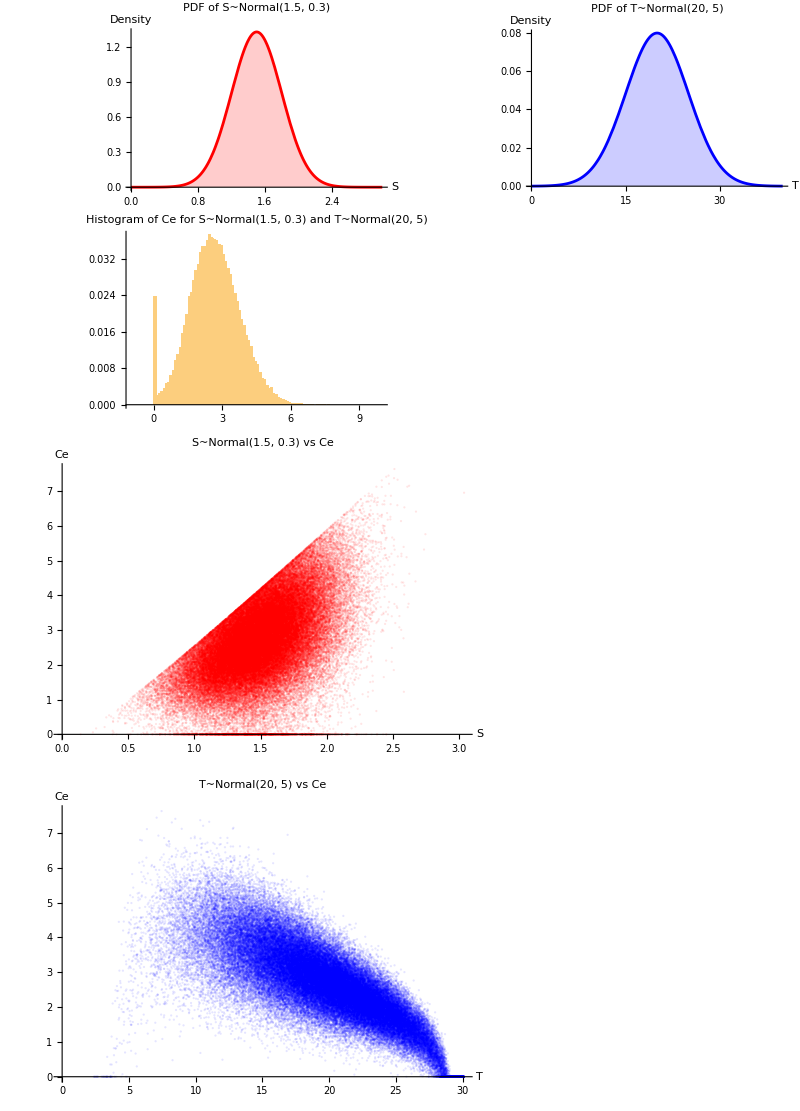

```mathematica
sensitivityAnalysis[1.5,0.3,20,5]  (*Custom mean and variance for S and T*)
```

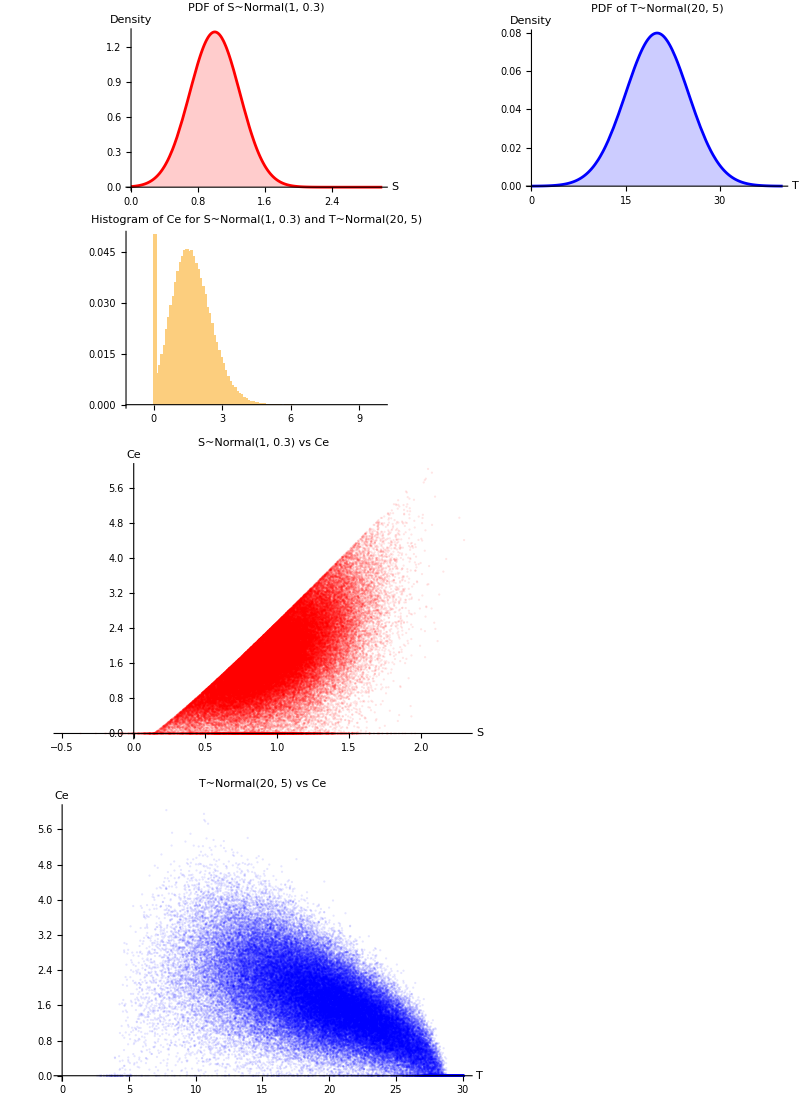

```mathematica
sensitivityAnalysis[1,0.3,20,5]  (*Custom mean and variance for S and T*)
```

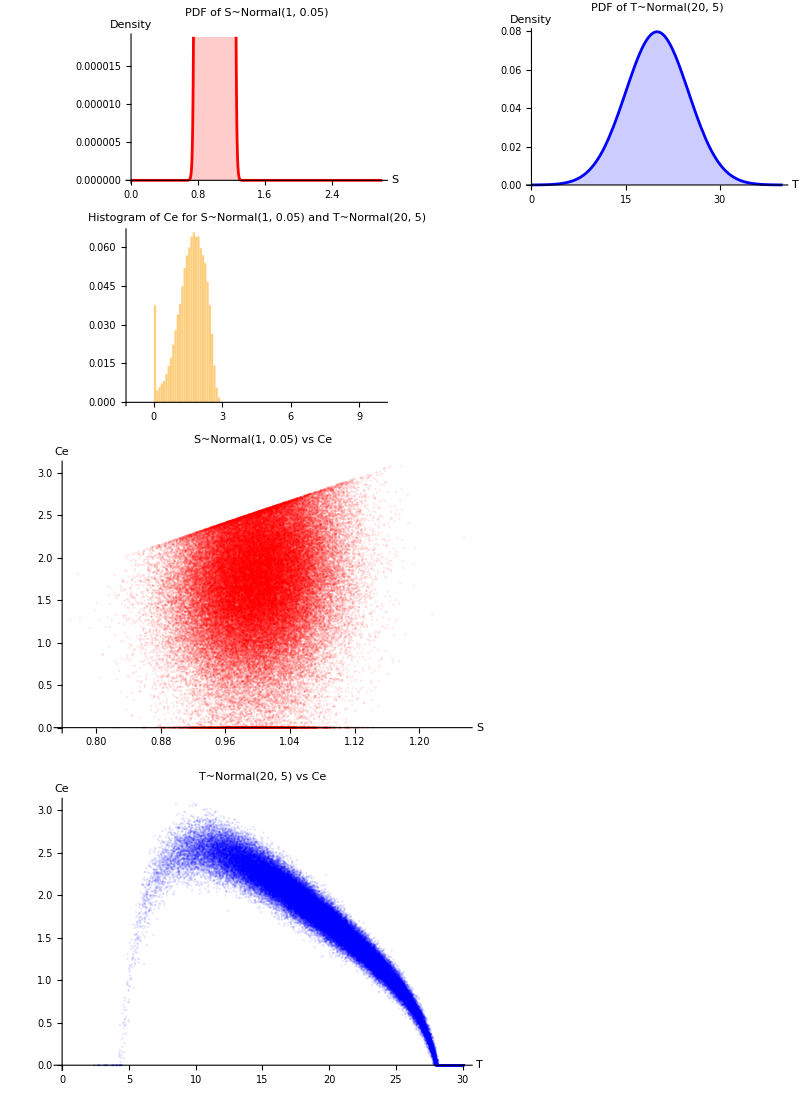

```mathematica
sensitivityAnalysis[1,0.05,20,5]  (*Custom mean and variance for S and T*)
```

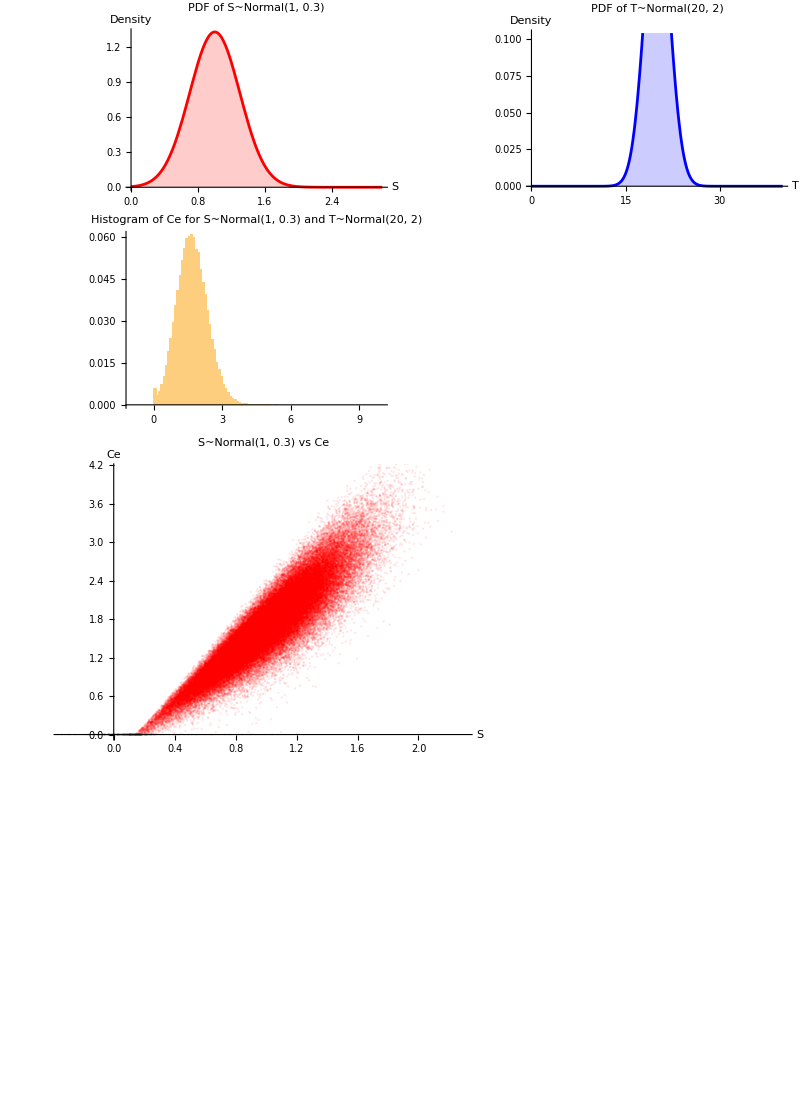

```mathematica
sensitivityAnalysis[1,0.3,20,2]  (*Custom mean and variance for S and T*)
```

```mathematica
(*Example usage with Gamma for S and Normal for T*)
sensitivityAnalysisGamma[2,1,20,5]
```

-Graphics-

```mathematica
sensitivityAnalysisGamma[1,1,20,5]
```

-Graphics-

```mathematica
sensitivityAnalysisGamma[3,0.2,20,5]
```

-Graphics-